William Kessel
HW3
ph105
204839956

The Langrangian is: -1/2 k x[t]^2+g m Cos[θ[t]] (a+x[t])+1/2 m (x'[t]^2+(a+x[t])^2 θ'[t]^2)

Euler Lagrange θ:
 m (a+x[t]) (g Sin[θ[t]]+2 x'[t] θ'[t]+(a+x[t]) θ''[t])==0

Euler Lagrange x:
 g m Cos[θ[t]]+m (a+x[t]) θ'[t]^2==k x[t]+m x''[t]

{{-19.5,19.5},{-50,1}}

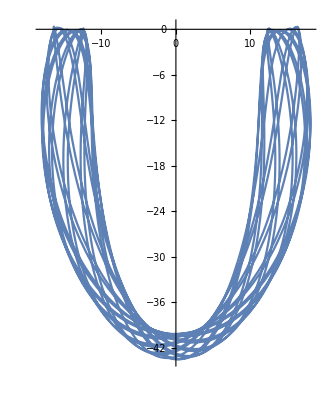

```mathematica
Remove["Global`*"]
SetAttributes[{m,k,g,a}, Constant]
(*spring equilibrium length a, stretches by x[t]*)
T=1/2 m(( x'[t])^2+(a+x[t])^2θ'[t]^2); 
U=-m g (a+x[t]) Cos[θ[t]]+1/2 k x[t]^2 ;

Lag=T-U;
Print["The Langrangian is: ", Lag//Simplify]
EL[q_]:= D[Lag, q]-Dt[D[Lag,D[q,t]], t]==0;

Print["Euler Lagrange θ:
 ", EL[θ[t]]//Simplify]
Print["Euler Lagrange x:
 ", EL[x[t]]//Simplify]

ellist={EL[x[t]], EL[θ[t]]};
iclist={x[0]==x0, θ[0]==θ0, x'[0]==v0, θ'[0]==ω0};
eqnlist=Join[ellist, iclist];
slist={x,θ};


(*paremeters*)
a=15;
k=7;
m=7;
g=10;
x0=0;
θ0=π/2;
v0=3;
ω0=0;
tmin=0;
tmax=150;
soln=NDSolve[eqnlist,slist, {t, tmin, tmax}][[1]];

(*Plot[x[t]/.soln, {t, tmin,tmax}, AxesLabel->{"t", "stretch legth"}]
Plot[θ[t]/.soln, {t, tmin, tmax}, AxesLabel->{"t", "θ"}]
*)
range={{-1.3a,1.3a},{-50,1}}
ParametricPlot[{(a+x[t])Sin[θ[t]], -(a+x[t])Cos[θ[t]]}/.soln, {t,0,150}]
traj[t_]:=ParametricPlot[{(a+x[t1])Sin[θ[t1]], -(a+x[t1])Cos[θ[t1]]}/.soln, {t1, Max[t-10, 0], t}]
spring[t_]:=ListLinePlot[{{0,0},{(a+x[t])Sin[θ[t]], -(a+x[t])Cos[θ[t]]}/.soln}, PlotStyle->{Black}]
mass[t_]:=Graphics[{PointSize[.03],Point[{(a+x[t])Sin[θ[t]], -(a+x[t])Cos[θ[t]]}/.soln]}]
pix[t_]:=Show[spring[t],mass[t],traj[t],PlotRange->range, AspectRatio->Full]
Animate[pix[t],{t, tmin,tmax}]
```

```mathematica
Remove["Global`*"]
SetAttributes[{L, R,g, m}, Constant]
T=1/2 m (x'[t]^2+y'[t]^2) ;
U=m g y[t];
lag=T-U;
(*coordinates*)
x[t_]=R Sin[θ[t]]+(L-R θ[t])Cos[θ[t]];
y[t_]=R Cos[θ[t]]-(L-R θ[t])Sin[θ[t]];

Print["The Langrangian is: ", lag//Simplify]

EL[q_]:= D[lag, q]- Dt[D[lag, D[q,t]],t]==0;

Print["EL θ: ", EL[θ[t]]//Simplify]


m=10;
R=5;
L=70;
g=10;
ω0=.4112;
tmin=0; 
tmax=100;
soln=NDSolve[{EL[θ[t]], θ[0]==0, θ'[0]==ω0}, θ, {t, tmin, tmax}];
(*Trajectory*)
plot:=ParametricPlot[{x[t], y[t]}/.soln,{t, tmin, tmax}, AxesLabel->{"y", x}]

(*mess around
Plot[{x[t]/.soln, y[t]/.soln},{t, tmin, tmax}]
*)
range={{-1.3 L, 1.3 L}, {-1.3 L, 1.3 L}};
circle:=Graphics[{Circle[{0,0}, R]}];
string[t_]:=ListLinePlot[{{R Sin[θ[t]], R Cos[θ[t]]}, {x[t],y[t]}}/.soln, PlotRange->range];
bob[t_]:=Graphics[{PointSize[.03], Point[{x[t],y[t]}/.soln]}];
pix[t_]:=Show[string[t], bob[t], circle,plot, AspectRatio->Automatic];
Animate[pix[t],{t, tmin, tmax}]
```

The Langrangian is: 1/2 m (-2 g R Cos[θ[t]]+2 g L Sin[θ[t]]+L^2 θ'[t]^2+R^2 θ[t]^2 θ'[t]^2-2 R θ[t] (g Sin[θ[t]]+L θ'[t]^2))

EL θ: m (L-R θ[t]) (g Cos[θ[t]]+R θ'[t]^2+(-L+R θ[t]) θ''[t])==0

```mathematica
Remove["Global`*"]
glist={G};
mlist=Table[m[i], {i,1,2}];
clist=Join[mlist,glist];
SetAttributes[clist, Constant];

r[i_][t_]={x[i][t],y[i][t]};
dist[a_,b_]=√((a-b).(a-b));
T=1/2 Sum[m[i] r[i]'[t].r[i]'[t],{i,1,2}];
U= -G Sum[m[i] m[j]/ dist[r[i][t],r[j][t]], {i,1,2},{j,i+1,2}];
lag=T-U;
lag//Simplify

EL[q_]:=D[lag, q]-Dt[D[lag, D[q,t]], t]==0;

ellist=Flatten[Table[{EL[x[i][t]], EL[y[i][t]]}//Simplify, {i, 1,2}]]
iclist=Flatten[Table[{x[i][0]==x0[i], y[i][0]==y0[i], x[i]'[0]==v0x[i], y[i]'[0]==v0y[i]}, {i,1,2}],1];
eqnlist=Join[ellist, iclist];
sollist=Flatten[Table[{x[i], y[i]}, {i, 1, 2}], 1];

(*parameters*)
G=1;
m[1]=25;
m[2]=.5;
x0[1]=0;
y0[1]=0;
x0[2]=100;
y0[2]=0;
v0x[1]=0;
v0y[1]=0;
v0x[2]=.1;
v0y[2]=.6;
t0=0;
t1=10000;

soln=NDSolve[eqnlist, sollist, {t,t0,t1}, MaxSteps->Infinity][[1]]

mtot=Sum[m[i], {i, 1, 2}];
rcm[t_]:=Sum[m[i] r[i][t]/mtot, {i, 1, 2}];

scale=0.03;
color={Orange,Blue};
extent=300;
range={{-extent, extent}, {-extent,extent}};
dot[i_]:={color[[i]], PointSize[scale √m[i]], Point[r[i][t]/.soln]};
cmdot[t_]:={Black, PointSize[0.02], Point[rcm[t]/.soln]};
plist[t_]:=Flatten[Table[dot[ i], {i, 1, 2}], 1];
traj:=ParametricPlot[{x[2][t],y[2][t]}/.soln,{t,t0,t1},PlotStyle->{Thin, Dashed,Red}]
plist[t_]=Join[plist[t],cmdot[t]]
points[t_]:=Graphics[plist[t]];
pix[t_]:=Show[{points[t],traj},Axes->True, PlotRange->range];
Animate[pix[t],{t,t0,t1}]
```

(G m[1] m[2])/(√((x[1][t]-x[2][t])^2+(y[1][t]-y[2][t])^2))+1/2 (m[1] ((x[1]'[t])^2+(y[1]'[t])^2)+m[2] ((x[2]'[t])^2+(y[2]'[t])^2))

{m[1] (-(G m[2] (x[1][t]-x[2][t]))/(((x[1][t]-x[2][t])^2+(y[1][t]-y[2][t])^2)^(3/2))-x[1]''[t])==0,m[1] (-(G m[2] (y[1][t]-y[2][t]))/(((x[1][t]-x[2][t])^2+(y[1][t]-y[2][t])^2)^(3/2))-y[1]''[t])==0,m[2] ((G m[1] (x[1][t]-x[2][t]))/(((x[1][t]-x[2][t])^2+(y[1][t]-y[2][t])^2)^(3/2))-x[2]''[t])==0,m[2] ((G m[1] (y[1][t]-y[2][t]))/(((x[1][t]-x[2][t])^2+(y[1][t]-y[2][t])^2)^(3/2))-y[2]''[t])==0}

{x[1]→InterpolatingFunction[{{0., 10000.}}, <>],y[1]→InterpolatingFunction[{{0., 10000.}}, <>],x[2]→InterpolatingFunction[{{0., 10000.}}, <>],y[2]→InterpolatingFunction[{{0., 10000.}}, <>]}

{RGBColor[1, 0.5, 0],PointSize[0.15],Point[{InterpolatingFunction[{{0., 10000.}}, <>][t],InterpolatingFunction[{{0., 10000.}}, <>][t]}],RGBColor[0, 0, 1],PointSize[0.0212132],Point[{InterpolatingFunction[{{0., 10000.}}, <>][t],InterpolatingFunction[{{0., 10000.}}, <>][t]}],GrayLevel[0],PointSize[0.02],Point[{0.980392 InterpolatingFunction[{{0., 10000.}}, <>][t]+0.0196078 InterpolatingFunction[{{0., 10000.}}, <>][t],0.980392 InterpolatingFunction[{{0., 10000.}}, <>][t]+0.0196078 InterpolatingFunction[{{0., 10000.}}, <>][t]}]}